# EWPT in the i2HDM

Comments: 1) Había un signo distinto en varios casos entre i2HDM y el VDDMM, 2) WWV1V2 existe en VDDMM.

## Loading package and Feynman rules

```mathematica
NotebookEvaluate["/home/bastilo/Dropbox/ProyectoVectorDM/ObliqueParameters/New/i2HDMEWPT/Defi2HDM.nb"];
Options[OneLoop];
```

Loading FeynCalc from /home/bastilo/.Mathematica/Applications/HighEnergyPhysics

HighEnergyPhysics`FeynCalc`MemoryAvailable`MemoryAvailable::shdw: Symbol MemoryAvailable appears in multiple contexts {HighEnergyPhysics`FeynCalc`MemoryAvailable`,System`}; definitions in context HighEnergyPhysics`FeynCalc`MemoryAvailable` may shadow or be shadowed by other definitions.

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading PHI

WARNING! Your FeynArts installation is not complete or the version you have cannot be used with this version of FeynCalc.
FeynArts can be downloaded at www.feynarts.de

Loading FeynArts, see www.feynarts.de for documentation

FeynArts not found. Please install FeynArts, e.g., in
/home/bastilo/.Mathematica
and reload FeynCalc
FeynArts can be downloaded from www.feynarts.de

```mathematica
(*Install["/home/bastilo/Documents/Programas/LoopTools-2.15/x86_64-Linux/bin/LoopTools"];
```

## Vaccum polarization Amplitudes

WW-polarization

```mathematica
-Graphics- + -Graphics- +-Graphics- +-Graphics-;
```

## Amplitudes

```mathematica
MWW1=Contract[WVCV1[q-l,l,μ].propH[q-l,MVC].WVCV1[-q+l,-l,ν].propH[l,MV1]];
MWW1L=OneLoop[l,%];
MWW1LPV=Simplify[PaVeReduce[MWW1L]];

MWW2=Contract[WVCV2b[q-l,l,μ].propH[q-l,MVC].WVCV2a[-q+l,-l,ν].propH[l,MV2]];
MWW2L=OneLoop[l,%];
MWW2LPV=Simplify[PaVeReduce[MWW2L]];

MWW3=Contract[WWVCVC[μ,ν].propH[q-l,MVC]];
MWW3L=OneLoop[l,%];
MWW3LPV=Simplify[PaVeReduce[MWW3L]];

MWW41=Contract[WWV1V1[μ,ν].propH[q-l,MV1]];
MWW41L=OneLoop[l,%];
MWW41LPV=Simplify[PaVeReduce[MWW41L]];

MWW42=Contract[WWV2V2[μ,ν].propH[q-l,MV2]];
MWW42L=OneLoop[l,%];
MWW42LPV=Simplify[PaVeReduce[MWW42L]];
```

## Sum of amplitudes

```mathematica
MWW=I/(16*π^4)Simplify[MWW1LPV+MWW2LPV+MWW3LPV+MWW41LPV+MWW42LPV];
ScalarProduct[FV[y,μ],FV[y,μ]]=1;
ScalarProduct[FV[q,μ],FV[y,μ]]=0;
ScalarProduct[y,y]=1;
ScalarProduct[q,y]=0;
```

## Getting the term proportional to gmunu

```mathematica
ΠWW=Expand[Contract[MWW,FV[y,μ].FV[y,ν]]];
ΠWWx=ΠWW/.ScalarProduct[q,q]->x;
```

## Replacing A0 to B0 and expanding B0(x,m1,m2)

```mathematica
(*SetOptions[A0,A0ToB0->True];
```

```mathematica
BB12=Normal[Series[B0[x,MV1^2,MV2^2],{x,0,1}]];
BB1C=Normal[Series[B0[x,MV1^2,MVC^2],{x,0,1}]];
BB2C=Normal[Series[B0[x,MV2^2,MVC^2],{x,0,1}]];
```

## The amplitude after replacements

```mathematica
WWF=Simplify[ΠWWx/.{B0[x,MV1^2,MV2^2]-> BB12}/.{B0[x,MV1^2,MVC^2]-> BB1C}]/.{B0[x,MV2^2,MVC^2]-> BB2C};
WW0=Expand[WWF]/.{x->0}
```

-(e^2 MV1^2 B_0(0,MV1^2,MVC^2))/(64 π^2 sw^2)-(e^2 MVC^2 B_0(0,MV1^2,MVC^2))/(192 π^2 sw^2)-(e^2 MV2^2 B_0(0,MV2^2,MVC^2))/(64 π^2 sw^2)-(e^2 MVC^2 B_0(0,MV2^2,MVC^2))/(192 π^2 sw^2)-(e^2 MV1^2 MVC^2 DB0(0,MV1^2,MVC^2))/(96 π^2 sw^2)+(e^2 MVC^4 DB0(0,MV1^2,MVC^2))/(192 π^2 sw^2)+(e^2 MV1^4 DB0(0,MV1^2,MVC^2))/(192 π^2 sw^2)-(e^2 MV2^2 MVC^2 DB0(0,MV2^2,MVC^2))/(96 π^2 sw^2)+(e^2 MVC^4 DB0(0,MV2^2,MVC^2))/(192 π^2 sw^2)+(e^2 MV2^4 DB0(0,MV2^2,MVC^2))/(192 π^2 sw^2)+(e^2 A_0(MV1^2))/(32 π^2 sw^2)+(e^2 A_0(MV2^2))/(32 π^2 sw^2)+(e^2 A_0(MVC^2))/(96 π^2 sw^2)-(e^2 MV1^2)/(96 π^2 sw^2)-(e^2 MV2^2)/(96 π^2 sw^2)-(e^2 MVC^2)/(48 π^2 sw^2)

ZZ-polarization

## -Graphics-+-Graphics-+-Graphics-+-Graphics-

## Amplitudes

```mathematica
MZZ1=Contract[ZVCVC[q-l,l,μ].propH[q-l,MVC].ZVCVC[-l,-q+l,ν].propH[l,MVC]];
MZZ1L=OneLoop[l,%];
MZZ1LPV=Simplify[PaVeReduce[MZZ1L]];

MZZ2=Contract[ZV1V2[l,q-l,μ].propH[q-l,MV2].ZV1V2[-l,-q+l,ν].propH[l,MV1]];
MZZ2L=OneLoop[l,%];
MZZ2LPV=Simplify[PaVeReduce[MZZ2L]];

MZZ3=Contract[ZZVCVC[μ,ν].propH[q-l,MVC]];
MZZ3L=OneLoop[l,%];
MZZ3LPV=Simplify[PaVeReduce[MZZ3L]];

MZZ41=Contract[ZZV1V1[μ,ν].propH[q-l,MV1]];
MZZ41L=OneLoop[l,%];
MZZ41LPV=Simplify[PaVeReduce[MZZ41L]];

MZZ42=Contract[ZZV2V2[μ,ν].propH[q-l,MV2]];
MZZ42L=OneLoop[l,%];
MZZ42LPV=Simplify[PaVeReduce[MZZ42L]];
```

## Sum of amplitudes

```mathematica
MZZ=I/(16*π^4)Simplify[MZZ1LPV+MZZ2LPV+MZZ3LPV+MZZ41LPV+MZZ42LPV];
ScalarProduct[FV[y,μ],FV[y,μ]]=1;
ScalarProduct[FV[q,μ],FV[y,μ]]=0;
ScalarProduct[y,y]=1;
ScalarProduct[q,y]=0;
```

Set::setraw: Cannot assign to raw object 1.

## Getting the term proportional to gmunu

```mathematica
ΠZZ=Expand[Contract[MZZ,FV[y,μ].FV[y,ν]]];
ΠZZx=ΠZZ/.ScalarProduct[q,q]->x;
```

## The amplitude after replacements

```mathematica
ZZF=Simplify[ΠZZx/.{B0[x,MV1^2,MV2^2]-> BB12}/.{B0[x,MV1^2,MVC^2]-> BB1C}]/.{B0[x,MV2^2,MVC^2]-> BB2C};
ZZMZ=Expand[ZZF]/.{x->MZ^2};
ZZ0=Expand[ZZF]/.{x->0}
```

-(e^2 MV1^2 B_0(0,MV1^2,MV2^2))/(64 π^2 cw^2 sw^2)-(e^2 MV2^2 B_0(0,MV1^2,MV2^2))/(192 π^2 cw^2 sw^2)-(cw^2 e^2 MVC^2 B_0(0,MVC^2,MVC^2))/(12 π^2 sw^2)-(e^2 MVC^2 B_0(0,MVC^2,MVC^2))/(48 π^2 cw^2 sw^2)+(e^2 MVC^2 B_0(0,MVC^2,MVC^2))/(12 π^2 sw^2)-(e^2 MV1^2 MV2^2 DB0(0,MV1^2,MV2^2))/(96 π^2 cw^2 sw^2)+(e^2 MV2^4 DB0(0,MV1^2,MV2^2))/(192 π^2 cw^2 sw^2)+(e^2 MV1^4 DB0(0,MV1^2,MV2^2))/(192 π^2 cw^2 sw^2)+(e^2 A_0(MV1^2))/(32 π^2 cw^2 sw^2)+(e^2 A_0(MV2^2))/(48 π^2 cw^2 sw^2)+(cw^2 e^2 A_0(MVC^2))/(12 π^2 sw^2)+(e^2 A_0(MVC^2))/(48 π^2 cw^2 sw^2)-(e^2 A_0(MVC^2))/(12 π^2 sw^2)-(e^2 MV1^2)/(96 π^2 cw^2 sw^2)-(e^2 MV2^2)/(96 π^2 cw^2 sw^2)-(cw^2 e^2 MVC^2)/(12 π^2 sw^2)-(e^2 MVC^2)/(48 π^2 cw^2 sw^2)+(e^2 MVC^2)/(12 π^2 sw^2)

```mathematica
(*SetOptions[A0,A0ToB0->False];
```

Divergence test

```mathematica
div={A0[MV1^2]->MV1^2*Div,A0[MV2^2]->MV2^2*Div,A0[MVC^2]->MVC^2*Div,B0[0,MV1^2,MV2^2]->Div,B0[0,MV1^2,MVC^2]->Div,B0[0,MV2^2,MVC^2]->Div,B0[0,MV1^2,MV1^2]->Div,B0[0,MV2^2,MV2^2]->Div,B0[0,MVC^2,MVC^2]->Div};
div1=Simplify[Coefficient[WW0/.div,Div]]*Div/(cw^2)
div2=Simplify[Coefficient[ZZ0/.div,Div]]*Div
```

(Div e^2 (MV1^2+MV2^2))/(64 π^2 cw^2 sw^2)

(Div e^2 (MV1^2+MV2^2))/(64 π^2 cw^2 sw^2)

```mathematica
div1-div2
```

0

Zγ-Amplitude polarization

-Graphics-

```mathematica
MZγ=Contract[AZVCVC[μ,ν].propH[q-l,MVC]];
MZγL=OneLoop[l,%];
MZγLPV=I/(16*π^4)Simplify[PaVeReduce[MZγL]];
```

## Getting the term proportional to gmunu

```mathematica
ΠZγ=Contract[MZγLPV,FV[y,μ].FV[y,ν]];
ΠZγx=ΠZγ/.ScalarProduct[q,q]->x;
```

## Expanding some amplitudes and replacing q^2->MZ^2

```mathematica
ZγF=Simplify[ΠZγx/.{B0[x,MV1^2,MV2^2]-> BB12}/.{B0[x,MV1^2,MVC^2]-> BB1C}]/.{B0[x,MV2^2,MVC^2]-> BB2C};
ZγMZ=Expand[ZγF]/.{x->MZ^2};
```

γγ-Amplitude

```mathematica
-Graphics--Graphics-
```

-Graphics- -Graphics-

```mathematica
Mγγ1=2*Contract[AVCVC[q-l,l,μ].propH[q-l,MVC].AVCVC[-l,-q+l,ν].propH[l,MVC]];
Mγγ1L=OneLoop[l,%];
Mγγ1LPV=Simplify[PaVeReduce[Mγγ1L]];

Mγγ2=Contract[AAVCVC[μ,ν].propH[q-l,MVC]];
Mγγ2L=OneLoop[l,%];
Mγγ2LPV=Simplify[PaVeReduce[Mγγ2L]];

MγγLPV=I/(16*π^4)Simplify[Mγγ1LPV+Mγγ2LPV];
```

## Getting the term proportional to gmunu

```mathematica
Πγγ=Contract[MγγLPV,FV[y,μ].FV[y,ν]];
Πγγx=Πγγ/.ScalarProduct[q,q]->x;
```

## Expanding some amplitudes and replacing q^2->MZ^2

```mathematica
γγF=Simplify[Πγγx/.{B0[x,MV1^2,MV2^2]-> BB12}/.{B0[x,MV1^2,MVC^2]-> BB1C}]/.{B0[x,MV2^2,MVC^2]-> BB2C}
γγMZ=Expand[γγF]/.{x->MZ^2};
γγMZ=Expand[γγF]/.{x->0}/.{B0[0,MVC^2,MVC^2]->Δ-Log[MVC^2/μ^2]}/.{A0[MVC^2]->(MVC^2)(Δ+1-Log[MVC^2/μ^2])}
```

-(e^2 (3 (4 MVC^2-x) B_0(x,MVC^2,MVC^2)+15 A_0(MVC^2)+12 MVC^2-2 x))/(72 π^2)

-(e^2 MVC^2 (Δ-log(MVC^2/μ^2)))/(6 π^2)-(5 e^2 MVC^2 (Δ-log(MVC^2/μ^2)+1))/(24 π^2)-(e^2 MVC^2)/(6 π^2)

T-parameter

```mathematica
Clear[T1]
```

```mathematica
T1=(WW0/(cw*MZ)^2-ZZ0/MZ^2)/α//Simplify
```

1/(192 π^2 α cw^2 MZ^2 sw^2)e^2 (16 cw^4 MVC^2 B_0(0,MVC^2,MVC^2)-16 cw^2 MVC^2 B_0(0,MVC^2,MVC^2)+3 MV1^2 B_0(0,MV1^2,MV2^2)+MV2^2 B_0(0,MV1^2,MV2^2)-3 MV1^2 B_0(0,MV1^2,MVC^2)-MVC^2 B_0(0,MV1^2,MVC^2)-3 MV2^2 B_0(0,MV2^2,MVC^2)-MVC^2 B_0(0,MV2^2,MVC^2)+4 MVC^2 B_0(0,MVC^2,MVC^2)+2 MV1^2 MV2^2 DB0(0,MV1^2,MV2^2)-MV2^4 DB0(0,MV1^2,MV2^2)-2 MV1^2 MVC^2 DB0(0,MV1^2,MVC^2)+MVC^4 DB0(0,MV1^2,MVC^2)-MV1^4 DB0(0,MV1^2,MV2^2)+MV1^4 DB0(0,MV1^2,MVC^2)-2 MV2^2 MVC^2 DB0(0,MV2^2,MVC^2)+MVC^4 DB0(0,MV2^2,MVC^2)+MV2^4 DB0(0,MV2^2,MVC^2)-2 (8 cw^4-8 cw^2+1) A_0(MVC^2)+2 A_0(MV2^2)+16 cw^4 MVC^2-16 cw^2 MVC^2)

```mathematica
DB0[0,1,2]
```

DB0(0,1,2)

```mathematica
DB0[0,300,400]
```

DB0(0,300,400)

```mathematica
DB0[0,1000,4500]
```

DB0(0,1000,4500)

```mathematica
(*Pag. 70 One-Loop Romao. DB0 were calculated with Mathematica*)
Repμ:={
A0[MV1^2]->(MV1^2)(Δ+1-Log[MV1^2/μ^2]),
A0[MV2^2]->(MV2^2)(Δ+1-Log[MV2^2/μ^2]),
A0[MVC^2]->(MVC^2)(Δ+1-Log[MVC^2/μ^2]),
B0[0,MV1^2,MV2^2]->Δ+1-(MV1^2Log[MV1^2]-MV2^2Log[MV2^2])/(MV1^2-MV2^2),
B0[0,MV1^2,MVC^2]->Δ+1-(MV1^2Log[MV1^2]-MVC^2Log[MVC^2])/(MV1^2-MVC^2),
B0[0,MV2^2,MVC^2]->Δ+1-(MV2^2Log[MV2^2]-MVC^2Log[MVC^2])/(MV2^2-MVC^2),
B0[0,MV1^2,MV1^2]->Δ-Log[MV1^2/μ^2],
B0[0,MV2^2,MV2^2]->Δ-Log[MV2^2/μ^2],
B0[0,MVC^2,MVC^2]->Δ-Log[MVC^2/μ^2],
DB0[0,MV1^2,MV2^2]->-(MV1^4-MV2^4+2 MV1^2 *MV2^2* Log[MV1^2/MV2^2])/(2 (MV1^2-MV2^2)^3),
DB0[0,MV1^2,MVC^2]->-(MV1^4-MVC^4+2 MV1^2 *MVC^2 *Log[MV1^2/MVC^2])/(2 (MV1^2-MVC^2)^3),
DB0[0,MV2^2,MVC^2]->-(MV2^4-MVC^4+2 MV2^2 *MVC^2* Log[MV2^2/MVC^2])/(2 (MV2^2-MVC^2)^3),
B0[MZ^2,MVC^2,MVC^2]->Δ-Log[MVC^2/μ^2]-(2 √(4*MVC^2-MZ^2)ArcTan[MZ/(√(4*MVC^2-MZ^2))])/MZ+2
};
```

```mathematica
(*Pag. 70 One-Loop Romao. DB0 were calculated with Mathematica*)
Rep:={
A0[MV1^2]->(MV1^2)(Δ+1-Log[MV1^2]),
A0[MV2^2]->(MV2^2)(Δ+1-Log[MV2^2]),
A0[MVC^2]->(MVC^2)(Δ+1-Log[MVC^2]),
B0[0,MV1^2,MV2^2]->Δ+1-(MV1^2Log[MV1^2]-MV2^2Log[MV2^2])/(MV1^2-MV2^2),
B0[0,MV1^2,MVC^2]->Δ+1-(MV1^2Log[MV1^2]-MVC^2Log[MVC^2])/(MV1^2-MVC^2),
B0[0,MV2^2,MVC^2]->Δ+1-(MV2^2Log[MV2^2]-MVC^2Log[MVC^2])/(MV2^2-MVC^2),
B0[0,MV1^2,MV1^2]->Δ-Log[MV1^2],
B0[0,MV2^2,MV2^2]->Δ-Log[MV2^2],
B0[0,MVC^2,MVC^2]->Δ-Log[MVC^2],
DB0[0,MV1^2,MV2^2]->-(MV1^4-MV2^4-2 MV1^2* MV2^2 *Log[MV1^2/MV2^2])/(2 (MV1^2-MV2^2)^3),
DB0[0,MV1^2,MVC^2]->-(MV1^4-MVC^4-2 MV1^2 *MVC^2 *Log[MV1^2/MVC^2])/(2 (MV1^2-MVC^2)^3),
DB0[0,MV2^2,MVC^2]->-(MV2^4-MVC^4-2 MV2^2 *MVC^2* Log[MV2^2/MVC^2])/(2 (MV2^2-MVC^2)^3),
B0[MZ^2,MVC^2,MVC^2]->Δ-Log[MVC^2]-(2 √(4*MVC^2-MZ^2)ArcTan[MZ/(√(4*MVC^2-MZ^2))])/MZ+2
};
```

The T parameter with Repμ

```mathematica
Clear[T2]
```

```mathematica
T2=T1/.Repμ/.{e->√(4π*α)}//Simplify
```

(2 MV1^4 MV2^2 MVC^2 log(MV2^2/μ^2)-2 MV1^4 MV2^2 MVC^2 log(MVC^2/μ^2)-5 MV1^4 MV2^2 MVC^2-2 MV1^4 MV2^2 MVC^2 log(MV2^2)-MV1^4 MV2^2 MVC^2 log(MV2^2/MVC^2)-6 MV1^4 MV2^2 MVC^2 log(MVC^2)-2 MV1^4 MV2^4 log(MV2^2/μ^2)+6 MV1^4 MV2^4 log(MV2^2)+5 MV1^4 MVC^4+2 MV1^4 MVC^4 log(MVC^2/μ^2)+2 MV1^4 MVC^4 log(MVC^2)+2 MV1^2 MV2^4 MVC^2 log(MVC^2/μ^2)+5 MV1^2 MV2^4 MVC^2+MV1^2 MV2^4 MVC^2 log(MV1^2/MVC^2)+6 MV1^2 MV2^4 MVC^2 log(MVC^2)-2 MV1^2 MV2^2 MVC^4 log(MV2^2/μ^2)+2 MV1^2 MV2^2 MVC^4 log(MV2^2)+MV1^2 MV2^2 (MV1^2-MVC^2) (MV2^2-MVC^2) log(MV1^2/MV2^2)-MV1^2 MV2^2 MVC^4 log(MV1^2/MVC^2)+MV1^2 MV2^2 MVC^4 log(MV2^2/MVC^2)+2 MV1^2 MV2^6 log(MV2^2/μ^2)-2 MV1^2 MV2^6 log(MV2^2)-8 MV1^2 MV2^4 MVC^2 log(MV2^2)+MV1^2 MV2^4 MVC^2 log(MV2^2/MVC^2)-5 MV1^2 MVC^6-2 MV1^2 MVC^6 log(MVC^2/μ^2)+2 MV1^2 MVC^6 log(MVC^2)-MV1^4 MV2^2 MVC^2 log(MV1^2/MVC^2)-4 MV1^4 log(MV1^2) (MV2^2-MVC^2)^2+MV1^4 MVC^4 log(MV1^2/MVC^2)-5 MV2^4 MVC^4-2 MV2^4 MVC^4 log(MVC^2/μ^2)-2 MV2^4 MVC^4 log(MVC^2)+5 MV2^2 MVC^6+2 MV2^2 MVC^6 log(MVC^2/μ^2)-2 MV2^2 MVC^6 log(MVC^2)-2 MV2^6 MVC^2 log(MV2^2/μ^2)+2 MV2^6 MVC^2 log(MV2^2)+2 MV2^4 MVC^4 log(MV2^2/μ^2)+2 MV2^4 MVC^4 log(MV2^2)-MV2^4 MVC^4 log(MV2^2/MVC^2))/(48 π cw^2 MZ^2 sw^2 (MV1^2-MV2^2) (MV1^2-MVC^2) (MV2^2-MVC^2))

The expansion of the T parameter in Δ

```mathematica
Clear[T3a]
```

```mathematica
T3a=Series[T2,{Δ,0,1}]//Simplify;
T3b=Series[T2,{Δ,0,0}]//Simplify;
```

```mathematica
(*NumT3b=Numerator[Normal[T3b]]
NumT3b/.{MV2->MVC};
```

Replacement  Δ -> Log[Λ^2/μ^2]  and   Δ -> Log[Λ^2/μ^2] -1

```mathematica
Clear[T30,T31]
```

```mathematica
T30=Normal[T2]/.{Δ->Log[Λ^2/μ^2]};
T31=Normal[T2]/.{Δ->Log[Λ^2/μ^2]-1};
```

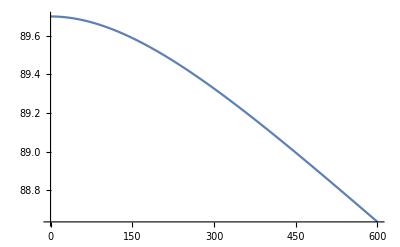

```mathematica
Block[{MV1,MV2,MVC,MZ,sw,cw,Λ,μ,α},
α=0.007;
MV2=700;
MVC=600;
sw=0.4;
cw=√(1-sw^2);
MZ=90.1;
Λ=10^100;
μ=MZ;
Plot[{T30},{MV1,0,600},PlotLegends->"Expressions"]]
```

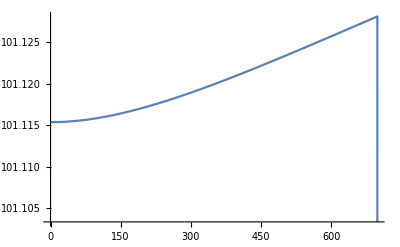

```mathematica
Block[{MV1,MV2,MVC,MZ,sw,cw,Λ,μ,α},
α=0.007;
MV2=699;
MVC=700;
sw=0.4;
cw=√(1-sw^2);
MZ=90.1;
Λ=10^100;
μ=MZ;
Plot[{T30},{MV1,0,699},PlotLegends->"Expressions"]]
```

The T parameter with Repμ

```mathematica
Clear[T2]
```

```mathematica
T20=T1/.Rep/.{e->√(4π*α)}//Simplify;
```

Replacement  Δ -> Log[Λ^2]  and   Δ -> Log[Λ^2] -1

```mathematica
Clear[T30,T31]
```

```mathematica
T300=Normal[T20]/.{Δ->Log[Λ^2]};
T310=Normal[T20]/.{Δ->Log[Λ^2]-1};
```

```mathematica
Block[{MV1,MV2,MVC,MZ,sw,cw,Λ,μ,α},
α=0.007;
MV2=300;
MVC=301;
sw=0.4;
cw=√(1-sw^2);
MZ=90.1;
Λ=100000000;
μ=MZ;
Plot[{T30,T31},{MV1,0,300},PlotLegends->"Expressions"]]
```

-Graphics-

S-parameter

```mathematica
Clear[S1]
Clear[S2]
Clear[S30]
Clear[S31]
```

```mathematica
S1=(4*cw^2*sw^2)/α((ZZMZ - ZZ0)/MZ^2-(cw^2-sw^2)/(cw*sw)*ZγMZ/MZ^2-γγMZ/MZ^2);
S2=S1/.Repμ/.{e->√(4π*α)}//Simplify;
```

## Replacing the Δ -> Log

```mathematica
S30=Normal[S2]/.{Δ->Log[Λ^2/μ^2]}//Simplify;
S31=Normal[S2]/.{Δ->Log[Λ^2/μ^2]-1}//Simplify;
```

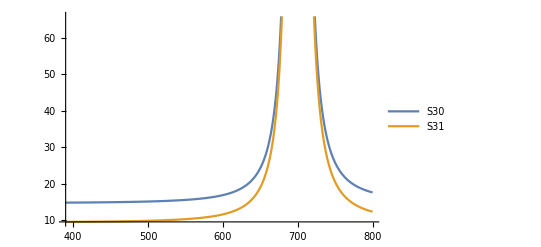

```mathematica
Block[{MV1,MV2,MVC,MZ,sw,cw,Λ,μ,α},
α=0.007;
MV2=700;
MVC=800;
sw=0.4;
cw=√(1-sw^2);
MZ=91;
Λ=2000;
μ=MZ;
Plot[{S30,S31},{MV1,390,800},PlotLegends->"Expressions"]]
```

## Trush

Pauli-Villars

```mathematica
(*Block[{m,Λ,F},F=10^10;m=1;Λ=10^3;
Plot[{F*(1/(p^2-m^2)),F*(1/(p^2-m^2)-1/(p^2-Λ^2))},{p,0,10^5},PlotLegends->"Expressions"]]
```

```mathematica
(*Block[{MZ,μ,MVC},∫_0^1 Log[(-x*(1-x)*MZ^2+MVC^2)/μ^2]ⅆx]
```

T from the i2HDM (paper)

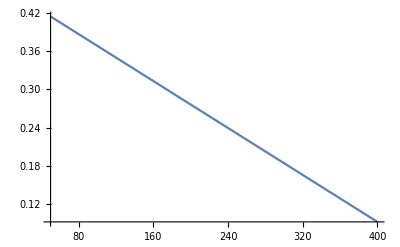

```mathematica
Block[{MH,MA,MS,α,v},
MA=400;
MH=500;
α=0.007;
v=256;
Plot[1/(24 π^2 α*v^2)(MH-MA)(MH-MS),{MS,50,400}]]
```

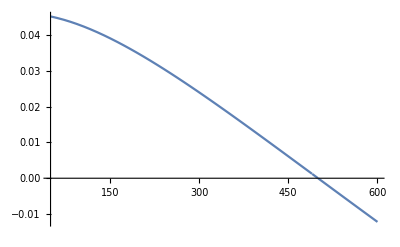

```mathematica
Block[{MH,MA,MS,α,v},
MA=490;
MH=500;
α=0.007;
v=256;
F[m1_,m2_]:=(m1^2+m2^2)/2-(m1^2*m2^2)/(m1^2-m2^2)Log[m1^2/m2^2];
Plot[1/(24 π^2 α*v^2)(F[MH,MA] + F[MH,MS]-F[MA,MS]),{MS,50,600}]]
```